```mathematica
ClearAll["Global`*","K"]
```

# Dynamics of a Plant Herbivore Model

In this report, I will aim to implement a pair of differential - difference equations (or DDEs) to model the interaction of a plant-herbivore system. DDEs are a type of differential equation in which it consists of a delayed argument in order to describe finite time changes in the populations for these two generic classes of species. Delay Differential Equations are important to consider in a population dynamics system because reproduction is not instantaneous. Typically, there is a time delay in which one species reaches full maturity in order to participate in the dynamic system. For example, a baby fox does not play a role in a predatory system with rabbits until possibly 3 months later when they grow to full size and are able to hunt.
	This model shown in the report was inspired by Senol Kartal, an associate professor in Nevsehir Haci Bektas Veil University, Turkey, as a way to understand the discrete and continuous effects between the two species behavior. The discrete components we used to obtain a system of differential equations with piecewise constant arguments as a way to provide a hybrid influence with difference equations. Through these set of differential-difference equations, the periodic nature was then prevalent through the analytical findings with the considerations of boundedness characters of the local and global stability conditions.

## The Differential-Difference Equations

x'(t)=r x(t) (1-(x(t))/K)-α x(t) y(t)
y'(t)=-sy(t)+βx(t)y(t)
where α, β,K, r , s >0

The variables:
x(t) and y(t) represent the population density of the plant and herbivore population respectively
α is the predation rate of the plant species
β is the conversion rate of the herbivore species
K is the environmental carrying capacity
r is the intrinsic growth rate relative to the plant species
s is the death rate of the herbivores

 The interactions:
 rx(t)(1-(x(t))/K) is the logistic term to denote an exponential growth capped at the environmental carrying capacity
 -sy(t) incorporates the continuous decay of the herbivore population
 αx(t)y(t) is the interaction term that represents the loss of a plant population due to herbivores
 βx(t)y(t) is the interaction term that represents the conversion factor for the growth of the herbivore population

### Stability Analysis

#### Steady States

```mathematica
DSolve[{0 == r*x[t]*(1-(x[t]/K))-α*x[t]*y[t], 0== -s*y[t]+β*x[t]*y[t]},{x[t],y[t]},t]
```

{{x[t]→s/β,y[t]→(r (-s+K β))/(K α β)},{x[t]→0,y[t]→0},{x[t]→K,y[t]→0}}

From the set of differential-difference equations, the following points are obtained as the equilibrium points:

E_0= (0,0) - Co-Extinction of both Plant and Herbivore Species

E_1=(K, 0) - The plant species reaches its carrying capacity in connection to its logistic growth rate

E_*= (s/β, r/α(1-s/Kβ)) - Co-Existence of both Plant and Herbivore Species

Note: For the positive Co-Existence steady state to exist,  Kβ > s

#### Conditions for Stability

In the paper this report is modeled after, the three equilibrium points are studied through the Jacobian to provide the stability conditions . It was given that E_0 and E_1 are saddle points as one eigenvalue satisfied being less than 1 while the other was greater than 1. As for the positive equilibrium, it yields in a characteristic equation that a Schur-Cohn criterion can be applied. The Schur-Cohn criterion yields with the indication of the positive equilibrium being locally asymptotically stable if s/K<β<(s+1)/K.

#### Direction Field

To explore the stability at each steady state of the system, the following plot provides a visualization aid to classify each scenario. We use the following parameter values in this case; however, they are arbitrary to showcase the stability is consistent in each case (α=0.6, β=0.01, K=5, r=0.2, s=0.02). The first steady state(0,0), E_0, and the second steady state(5,0),E_1, are saddle points. The co-existence steady state (2, 0.2) is locally asymptotically stable as its spiral behavior closes inward. We can refer back to the stability conditions to ensure that this particular case makes sense. For the co-extinction and max-carrying capacity equilibrium points, they are indeed saddle points. For the co-existence equilibrium point, we satisfy the condition that s/K<β<(s+1)/K (or 0.004<0.01<0.204) and such behavior of a locally asymptotically stable point is valid.

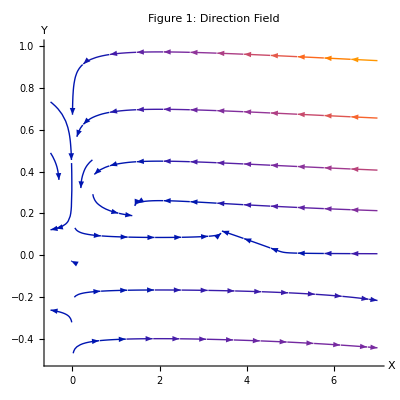

```mathematica
α=0.6;
β=0.01;
K=5; 
r=0.2; 
s=0.02;
f[x_,y_]= r*x*(1-(x/K))-α*x*y;
g[x_,y_]=-s*y+β*x*y;
df = StreamPlot[{f[x,y],g[x,y]},{x,-0.5,7},{y,-0.5,1},PlotLabel->"Figure 1: Direction Field", Frame->False,Axes->True,AspectRatio->1,Frame->True,AxesLabel->{"X","Y"}]
```

### Original System

Here, we investigate the normal behavior of the differential equations, or without delay. It is with interest that we look at the case of when both population can co-exist in the same environment. The parameters are kept the same as they were in the Direction Field section and it displays a logistic growth behavior for the plant population in the early time values then decreases to a plateau, or s/β (Refer to Figure 2). As for the herbivore population, the display showcases as slight dip in the population for the first time values then slightly increases to a plateau, or r/α(1-s/Kβ). The tradeoff for plant growth and herbivore decay is biologically feasible and can be explained through the idea of limited resources. In the first few moments of time, the plant population is reaching its maturity status and so the herbivores are dying from lack of food and since there is a decrease in herbivores the plants can continue to thrive. That is until the herbivore population reach this turning point in their density where they are able to feed off the plant population and reach this harmonious stable behavior for the rest of time. 
	Interestingly enough, the moment the environmental carrying capacity is increased to a larger values (i.e. 200, Refer to Figure 3), the models begins to exhibit a periodic behavior in both the plant and herbivore species. Over time, the plant population experiences a periodic decay with a consistent low value in every period, whereas the herbivore population has a consistent periodic behavior. 
	In both cases, the Herbivore population exhibits a questionable biological behavior. For every periodic iteration, the population density reaches a near-zero value, so it becomes questionable to think about how the population begins to reproduce enough to increase from near extinction. Interestingly, the plant population will continue to decay in an oscillatory fashion towards the stable steady-state value

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

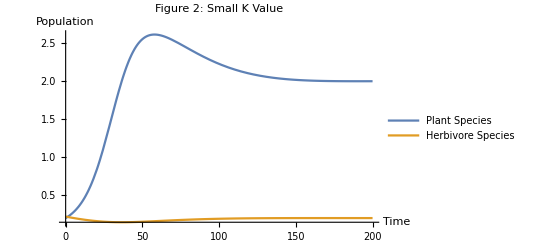

```mathematica
α=0.6;
β=0.01;
K=5; 
r=0.2; 
s=0.02; 
x0=0.2;
y0=0.22;
soln = NDSolve[{x'[t]==r*x[t]*(1-(x[t]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t]*y[t], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,-3,800}]
Plot[Evaluate[{x[t],y[t]}/. soln], {t,0,200},PlotLabel->"Figure 2: Small K Value", PlotRange->All, AxesLabel->{Time, Population}, PlotLegends->{Plant Species, Herbivore Species}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

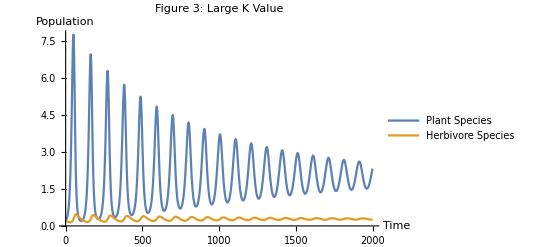

```mathematica
α=0.7;
β=0.01;
K=200; 
r=0.2; 
s=0.02; 
x0=0.2;
y0=0.22;
soln = NDSolve[{x'[t]==r*x[t]*(1-(x[t]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t]*y[t], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,-3,2000}]
Plot[Evaluate[{x[t],y[t]}/. soln], {t,0,2000},PlotLabel->"Figure 3: Large K Value", PlotRange->All, AxesLabel->{Time, Population}, PlotLegends->{Plant Species, Herbivore Species}]
```

#### Manipulation of Parameters for Parametric Plot

Below, I investigate the behavior of both populations side by side in a Population vs Time and a Plant population vs Herbivore Population plot where the parameter values can be adjusted for exploration. For starting values in the Population vs Time plot, the parameters are the following: α=0.4, β=0.6, K=80, r=0.5, and s=0.6. Due to the predation, conversion, and intrinsic growth rates being relatively near the same value, we can observe a somewhat increase-decrease behavior in the population in which the plant population reaches its peak first and, in turn, it allows for the herbivore population to reach its peak for each oscillation. However, with the given choice of parameters, the intrinsic growth rate of the plant population is slightly lower than the predation rate, so we observe periodic decay in the plant population and due to the interaction terms inspired by the plant and herbivore food chain, the herbivore population experiences a periodic decay as well. Over time, this periodic solution will tend towards our stable point--once again validating the model’s stability behavior(Refer to Figure 4). Lastly, it can be seen once again that increasing the carrying capacity does have an effect on how the system behaves, in this particular case, it minimizes the periodic decay of the both populations to converge longer. 
	Now, looking at the Plant vs Herbivore plot (Refer to Figure 5), the set parameters for the initial plot are as given: α=0.1, β=0.2, K=10, r=0.3, and s=0.2. From the initial values (x_0=0.2, y_0=0.22), the curve spirals inward to the co-existing stable steady state. For the given values, we will obtain that the point will be E_*= (s/β, r/α(1-s/Kβ)), or (1, 2.7).

```mathematica
ClearAll["Global`*","K"]
x0=0.2;
y0=0.22;
tF=500;
pSoln1 = ParametricNDSolveValue[{x'[t]==r*x[t]*(1-(x[t]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t]*y[t], x[0]==x0,y[0]==y0}, {x,y}, {t,tF}, {α,β,K,r,s}];
Manipulate[Plot[Evaluate[#[t]&/@pSoln1[α,β,K,r,s]],{t,0,100},PlotLabel->"Figure 4: Population vs Time", PlotRange->{All,All}, Frame->True, FrameLabel-> {"Time", "Population"}, PlotLegends->{Plant Species, Herbivore Species}],{{α, 0.4},0,1}, {{β,0.6},0,1}, {{K,80},1,250}, {{r,0.5},0,1}, {{s,0.6},0,1}]
Manipulate[ParametricPlot[Evaluate[#[t]&/@pSoln1[α,β,K,r,s]],{t,0,200}, AspectRatio->Automatic,PlotRange->{All,All}, Frame->True,FrameLabel-> {"x(t)", "y(t)"},PlotLabel->"Figure 5: Plant vs Herbivore Parametric Curve"]/. Line[x_] :> {Arrowheads[{0., 0.05, 0.05, 0.05, 0.}], Arrow[x]},{{α, 0.1},0,1}, {{β,0.2},0,1}, {{K,10},1,250}, {{r,0.3},0,1}, {{s,0.2},0,1}]
```

### Constant Delays

Constructing models with DDEs allows for the use of delays or time lags for which it can indicate the longevity of hidden processes such as maturation, conversion, infection periods, etc. In this discrete system of equations, it allows for the evolution at a given time to be dependent on the previous time-steps, or history, in addition to the current time step. Given the context of the plant and herbivore system, my model choice indicates a time delay in the plant growth by a constant delay of 2(i.e. ‘t-2’). Applying this particular constant delay on the plant growth suggests a maturation for the plant species as 2 months are needed for a plant to reach full growth and become a food source for the herbivores. Similarly, for the herbivore species, there is a constant delay of 3 (i.e. ‘t-3’). In the same manner, this suggests another maturation rate for the herbivore population to be considered in the conversion interaction with mature plants. Herbivores will reach mature status after 3 months as infant herbivore species are dependent on their mothers rather than plants for a food source. From a biological standpoint, the model with constant delays was supported by life-cycle behavior. 
	In the initial time step, or t=0, there is a logical issue with getting population values at negative time-step values. At time zero for the first instance, the model requires information from 2-3 steps back. We construct a history function that would describe the behavior for time values less than 0. In such choice of a history function, I had to be aware of the sensitivity the model might have to the changes. In the end, a quadratic function of time was used for both the plant and herbivore species as it seemed most feasible. Various other history functions were implemented as well such as absolute value functions and linear functions. The motive for these choices were backed up by the idea of needing a positive population for past documentation. It is not biologically feasible to say the past can observe negative populations and then somehow experience oscillations. Instead, the model needed a past that suggested a continuous, smooth, and differentiable curve at all time steps prior to 0. 
	Similar to the original set of differential equations, the time delay displays similar behavior in the trajectory of the plant and herbivore population over time -- an opposing increase-decrease behavior in both trends to then plateau(Refer to Figure 6). Then, the moment we introduce a higher environmental carrying capacity we observe periodic behavior; however, the only difference is that the plant population experiences a periodic growth rather than periodic decay(Refer to Figure 7). This suggests that in time the plant population requires a suffrage of the herbivore population and have it in a periodic stasis in order for the plant to thrive on its own over time. 
	Interestingly, the paper suggests the condition for which the system undergoes Neimark-Sacker bifurcation. If 1/K=β/(s+1), then our system behaves in a closed curve from the fixed point. With the given parameters for the second plot, or α=0.6, β-0.01, K=102, r=0.2, s=0.02, we achieve the Neimark-Sacker bifurcation condition.

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

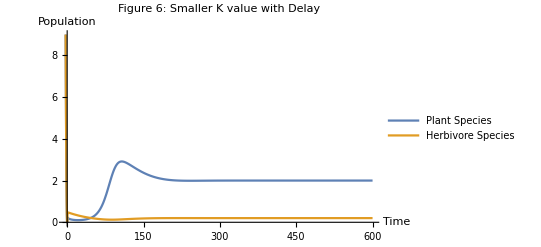

```mathematica
α=0.6;
β=0.01;
K=5; 
r=0.2; 
s=0.02; 
x0=0.2;
y0=0.22;
soln = NDSolve[{x'[t]==r*x[t-2]*(1-(x[t-2]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t-3]*y[t-3], x[t/;t≤0]==t^2, y[t/;t≤0]==t^2, x[0]==x0,y[0]==y0},{x[t],y[t]},{t,-3,600}]
Plot[Evaluate[{x[t],y[t]}/. soln], {t,-3,600}, PlotLabel->"Figure 6: Smaller K value with Delay", PlotRange->All, AxesLabel->{Time, Population}, PlotLegends->{Plant Species, Herbivore Species}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

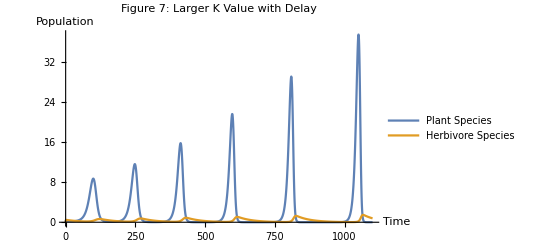

```mathematica
α=0.6;
β=0.01;
K=102; 
r=0.2; 
s=0.02; 
x0=0.2;
y0=0.22;
soln = NDSolve[{x'[t]==r*x[t-2]*(1-(x[t-2]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t-3]*y[t-3], x[t/;t≤0]==t^2, y[t/;t≤0]==t^2, x[0]==x0,y[0]==y0},{x[t],y[t]},{t,-3,1100}]
Plot[Evaluate[{x[t],y[t]}/. soln], {t,0,1100}, PlotLabel->"Figure 7: Larger K Value with Delay", PlotRange->All, AxesLabel->{Time, Population}, PlotLegends->{Plant Species, Herbivore Species}]
```

#### Manipulation of Parameters for Parametric Plot

Given the interpretation of the effects of a constant delay on the pair of differential-difference equations, it also goes to show the system exhibits a unique behavior. In the first plot(Refer to Figure 8), the following parameters are set: α=0.1, β=0.2, K=75, r=0.35, and s=0.45. Similar to the set or ordinary differential equations, the model contains a cyclical behavior in the populations such that there is a repeating effect; however, unlike the original case where the plot displayed a periodic decay, we observe a delayed periodic growth in both populations. The key difference is that, for this delayed model, we have a prolonged intermediate section between oscillations in comparison to the original model. The spaced out oscillations portrays the time delay for the growth and conversion of the plant and herbivore, respectively, and indicates a longer lag for which a plant population can provide for the growth of the herbivore population.  
	Over a long period of time, the delayed system consistently exhibits a periodic-orbiting behavior for the trajectories of both the plant and herbivore population. When closely looked at, there are a certain number of oscillations before it begins to repeat its same structure. Similarly, with the parametric curve(Refer to Figure 9), the trajectories are following a closed curve with limiting behavior in the overall stability; nonetheless, it consistently centralize equilibrium point of interest.

```mathematica
x0=0.2;
y0=0.22;
tF=6000;
pSoln2 = ParametricNDSolveValue[{x'[t]==r*x[t-2]*(1-(x[t-2]/K))-α*x[t]*y[t],
		 y'[t]==-s*y[t]+β*x[t-3]*y[t-3], x[t/;t≤0]==t^2, y[t/;t≤0]==t^2, x[0]==x0,y[0]==y0}, {x,y}, {t,tF}, {α,β,K,r,s}];
Manipulate[Plot[Evaluate[#[t]&/@pSoln2[α,β,K,r,s]],{t,0,tF}, PlotRange->{All,All}, PlotLabel->"Figure 8: Population vs Time with Delay", PlotLegends->{Plant Species, Herbivore Species}],{{α, 0.1},0,1}, {{β,0.2},0,1}, {{K,75},1,250}, {{r,0.35},0,1}, {{s,0.45},0,1}]
Manipulate[ParametricPlot[Evaluate[#[t]&/@pSoln2[α,β,K,r,s]],{t,0,tF}, PlotLabel->"Figure 9: Parametric Curve with Delay", PlotRange->All, Frame->True,FrameLabel-> {"x(t)", "y(t)"},PlotLabel->{"Parametric Plot: Plant vs Herbivore"}]/. Line[x_] :> {Arrowheads[{0., 0.05, 0.05, 0.05, 0.}], Arrow[x]},{{α, 0.1},0,1}, {{β,0.2},0,1}, {{K,10},1,250}, {{r,0.3},0,1}, {{s,0.2},0,1}]
```

### Observations and Discussion

Overall, this paper aims to describe the interacting behavior of a prey-predatory system in the scope of a generic plant and herbivore population. The stability of the system was identified and confirmed through the assumption of Schur-Cohn criterion from the paper analytically and graphically. In the scope of a population-dynamics system, there were two main approaches that were attempted to understand the model behavior. In a simple approach to view the continuous time effect, the set of ordinary differential equations described how the system would behave if the model considered the population at that same moment in time. This approach did well in describing the oscillatory behavior that these two species should exhibit over time -- such that as one increases the other should be decreasing. What this method fails to realize is the biological factors of herbivore gestation as well as plant maturation. In a new model, these biological factors are taken into consideration through the incorporation of difference equations to provide a delaying effect. The model accounts for a two month delay for the plant species to reach its full maturity and, similarly, the model accounts for a 3 month gestation delay for an infant herbivore to ingest the plant species. This new model now provides a more accurate representation of the biological interaction at hand as it yet again converges to the co-existing steady state over time in a periodic cycle. The plant population has growth at a consistent rate with respect to the carrying capacity while the herbivore population remains in a static periodic orbit. While this delayed model does a better job at representing the delaying factors, its behavior can still appear farfetched for the herbivore population. From Figure 7, the biological concern is set around the idea of the herbivore population density reaching near extinction, but still being able to behavior in a oscillatory fashion. There are strong assumptions made in this model such as what if those last few of the herbivore species are all male and cannot reproduce or they are older females who no longer have the ability to reproduce. These concerns are not directly addressed in the model as it treats each individual pair of the herbivore species the ability to reproduce at its convenience. Nonetheless, this model exhibits proper behavior overall for how the system should behave with the conversion, death, and growth rates between both species. 
	In addition, many factors of the stability conditions root from three main parameters: the conversion rate, the death rate, and the carrying capacity. Between these three parameters, it can be interestingly noted that the alterations of any of these can cause the system to converge to a stable point. One in particular was the carrying capacity of the plant species as it determined the Neimark-Sacker bifurcation. The moment K became larger and larger is when I noticed, alongside the paper, that the system enters in a stable limited cycle. Around 100 is typically when it experienced oscillations and then once passed a certain value, it would experience a growth for every oscillation. For this model, in particular for both the ordinary and delayed system, K has a great effect on whether or not this system is stable and whether or not there is control to both these two populations.
	In consideration of the other variables, these were the notes I made on how each of the parameters affected the overall system (Refer to Table 1 below). 
	α | affects the amplitude (vertically)
β | affects the number of oscillations 
in a time frame (horizontally)
K | affects the compression/decay of the 
periodic trend (vertically)
r | affects the number of oscillations in a 
time frame (horizontally)
s | affects the amplitude and the number of 
oscillation in a given 
time frame(vertically and horizontally)
	Overall, I would move forward with the time delayed system of differential equations as it contributes to understanding the biology aspects with maturity and gestation of the species. Using this interpretation is definitely a great start, but there are definitely a few things I would like to explore later and incorporate in the model. For starters, I would like to try and interpret it as it would be in nature where there is randomness incorporated with stochastic processes such as plant growth, species movement, birth, death, and how that can play a role to the overall plant population. This would probably be the first step in mimicking the randomness that nature presents itself in and then I would like to verify its accurateness in a analysis portion. This would require me to collect data and it would be really interesting if I could go to the field and observe/collect data on both a particular plant and herbivore species. Another change that would be interesting would be of a complex system where I can think of an ecosystem in connection to a food chain, so that other species in the area also affect or contribute to the decay/growth of the other species. Of course, this would be a larger scale problem as it would require to work alongside an ecologist who knows a particular field well and it would require a strong data collection stage to establish the growth, birth, death, conversion, etc. rates of all populations given their interactions. In either of these models, I would definitely continue more with a delayed differential equation because plant growth are not always just instantaneous/continuous. Nature is bounded to the principle of randomness and thus must be matched with random properties in the model. Ultimately, I would move forward with a delayed differential equation with stochastic properties to mimic this particular biological system.

## References

E. M. Elsayed, Qamar Din. (2019) Period-doubling and Neimark–Sacker bifurcations of plant–herbivore models. Advances in Difference Equations 2019:1.
Crossref

JOYDEV CHATTOPADHAYAY, RAMRUP SARKAR, MARIA ELENA FRITZSCHE - HOBALLAH, TED C . J . TURLINGS, LOUIS - FÉLIX BERSIER, Parasitoids may Determine Plant Fitness—A Mathematical Model Based on Experimental Data, Journal of Theoretical Biology, Volume 212, Issue 3, 2001, Pages 295 - 302, ISSN 0022 - 5193, https : // doi . org/10.1006/jtbi .2001 .2374 . (https : // www . sciencedirect . com/science/article/pii/S0022519301923744)

Qamar Din, M. Sajjad Shabbir, M. Asif Khan, Khalil Ahmad. (2019) Bifurcation analysis and chaos control for a plant–herbivore model with weak predator functional response. Journal of Biological Dynamics 13:1, pages 481-501.

Wikipedia contributors. (2020, December 29). Stable polynomial. In Wikipedia, The Free Encyclopedia. Retrieved 21:02, May 13, 2021, from https://en.wikipedia.org/w/index.php?title=Stable_polynomial&oldid=997010905

Wikipedia contributors. (2021, April 9). Schur polynomial. In Wikipedia, The Free Encyclopedia. Retrieved 21:02, May 13, 2021, from https://en.wikipedia.org/w/index.php?title=Schur_polynomial&oldid=1016783603

Wikipedia contributors. (2020, December 29). Hurwitz polynomial. In Wikipedia, The Free Encyclopedia. Retrieved 21:02, May 13, 2021, from https://en.wikipedia.org/w/index.php?title=Hurwitz_polynomial&oldid=997009321